```mathematica
h:=2/3 h1 Jx^(3/2) Cos[3 (ϕx+(0+Δ+η/2) s 2π)]+2/3 h2 Jy^(3/2) Cos[3 (ϕy+(0+Δ-η/2) s 2π)]+Jx √Jy (h11 Cos[2 ϕx+ϕy+δ1+(2(0+Δ+η/2)+(0+Δ-η/2))s 2π])+√Jx Jy (h12 Cos[ϕx+2 ϕy+δ2+((0+Δ+η/2)+2(0+Δ-η/2))s 2π])
ϕxstr=D[h,Jx];
Jxstr=-D[h,ϕx];
ϕystr=D[h,Jy];
Jystr=-D[h,ϕy];
Jxstrd=Jxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
Jystrd=Jystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕxstrd=ϕxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕystrd=ϕystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
```

```mathematica
inputpr=({Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==Jxv,Jy[0]==Jyv,ϕx[0]==ϕxv,ϕy[0]==ϕyv}/.{h1->h1,h2->h2,R->1,h11->h11,h12->h12,η->η,Δ->Δ,δ1->δ1,δ2->δ2,s->t});
```

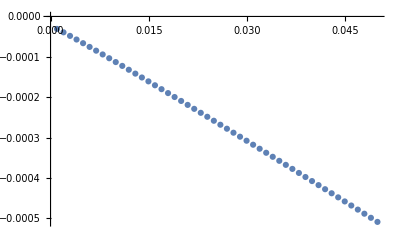

```mathematica
inloc=inputpr/.{h1->.0001,h2->.0001,R->1,h11->0.1,h12->.0001,η->.05,Δ->.0001,δ1->0,δ2->0,Jxv->.005,ϕxv->0,ϕyv->π};
aplot=ListPlot[Table[{Mean[Table[Abs[((Jy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jyv,0.001,0.05,.001}]]
```

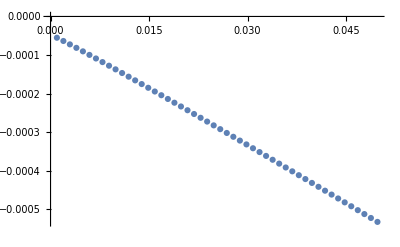

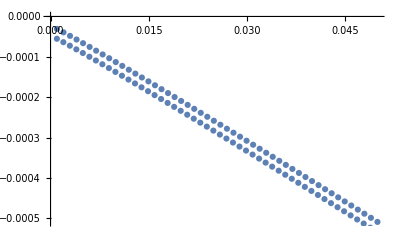

```mathematica
inloc=inputpr/.{h1->.0001,h2->.0001,R->1,h11->0.1,h12->.0001,η->.05,Δ->.0001,δ1->0,δ2->0,Jxv->.01,ϕxv->0,ϕyv->π};
bplot=ListPlot[Table[{Mean[Table[Abs[((Jy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jyv,0.001,0.05,.001}]]
Show[{aplot,bplot}]
```

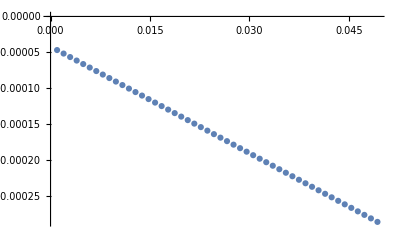

```mathematica
inloc=inputpr/.{h1->.0001,h2->.0001,R->1,h11->0.1,h12->.0001,η->.05,Δ->.0001,δ1->0,δ2->0,Jyv->.01,ϕxv->0,ϕyv->π};
ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv,0.001,0.05,.001}]]
```

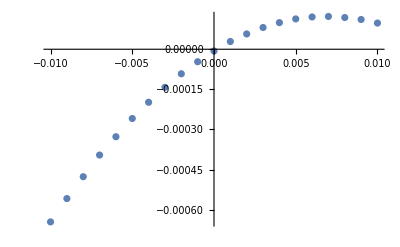

```mathematica
inloc=inputpr/.{h1->.0001,h2->.0001,R->1,h11->f2v,h12->.0001,η->.05,Δ->.0001,δ1->0,δ2->0,Jyv->.005,ϕxv->0,ϕyv->π};
ListPlot[Table[{f2v,(1/x Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv,0.001,0.009,.1}],{1,x},x])/.{x->10000}},{f2v,-.01,.01,0.001}]]
```

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->0.1,f2v->0,pv->f2v,rv->0,k11->0,k12->0};
Fit[Table[{f2v,(1/x Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x])/.{x->10000}},{f2v,-1,1,0.1}],{1,x},x]
```

2.85807×10^-17+0.75 x

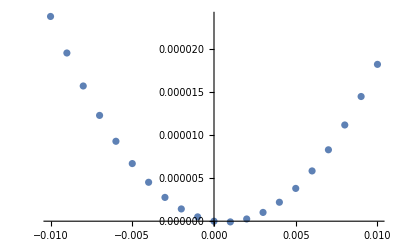

```mathematica
inloc=inputpr/.{Jxv->Jxv1,Jyv->1-Jxv1,ϕxv->π/2,ϕyv->0,δv->.1,f2v->0,pv->0,rv->0,k11->0,k12->f2v};
ListPlot[Table[{f2v,(Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv1,0.1,0.9,.1}],{1,x},x])/.{x->0}},{f2v,-.01,.01,0.001}]]
```

```mathematica
0.001 - 5.6438
```

```mathematica
5.6438 Sqrt[5]
```

12.6199

```mathematica
13.25 - 0.001, .1
```

```mathematica
13.25 Sqrt[2]
```

18.7383

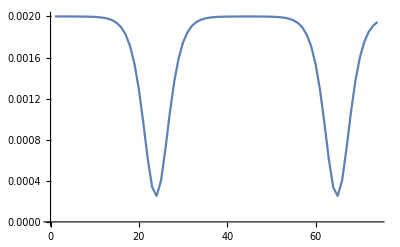

```mathematica
inloc=inputpr/.{h1->0,h2->0,R->1,h11->8.9446,h12->0,η->.0001,Δ->0,δ1->0,δ2->0,Jxv->.002,ϕxv->0,ϕyv->π};
Table[ListPlot[Table[Jx[t]/.Flatten[NDSolve[inloc/.{p->p,Jyv->0.002},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,73.8}]]/.{t->t1},{t1,0,73.8,1}],Joined->True],{p,.295,.295,0.001}]
```

```mathematica
порядок величины - Sqrt[J]h11~(0.4+0.2η)
```

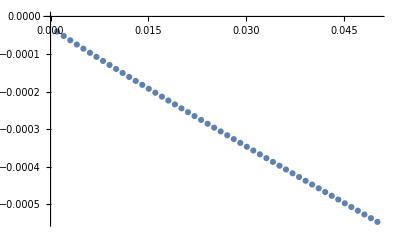

```mathematica
inloc=inputpr/.{h1->.0001,h2->.0001,R->1,h12->0.1,h11->.0001,η->.05,Δ->.0001,δ1->0,δ2->0,Jyv->.005,ϕxv->0,ϕyv->π};
aplot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv,0.001,0.05,.001}]]
```

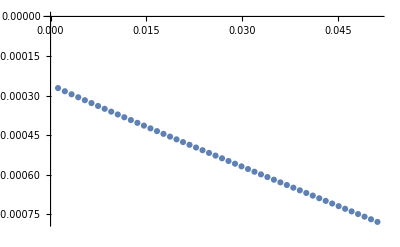

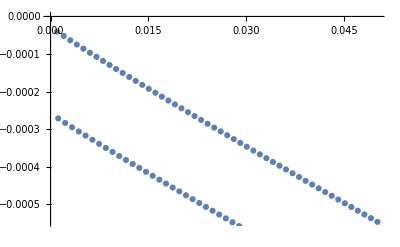

```mathematica
inloc=inputpr/.{h1->.0001,h2->.0001,R->1,h12->0.1,h11->.0001,η->.05,Δ->.0001,δ1->0,δ2->0,Jyv->.05,ϕxv->0,ϕyv->π};
bplot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv,0.001,0.05,.001}]]
Show[{aplot,bplot}]
```

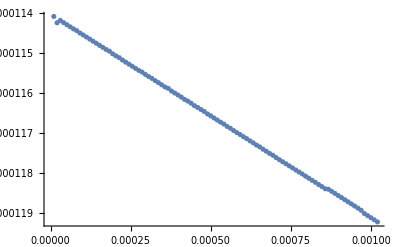

```mathematica
inloc=inputpr/.{h1->0,h2->0,R->1,h11->0,h12->0.1,η->.05,Δ->.0001,δ1->0,δ2->0,Jxv->.01,ϕxv->0,ϕyv->π};
aplot=ListPlot[Table[{Mean[Table[Abs[((Jy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jyv,0.00001,0.001,.00001}]]
```

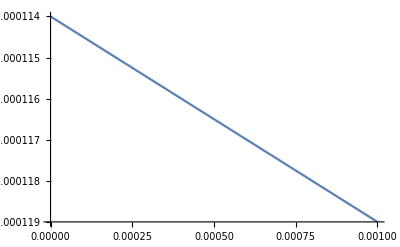

```mathematica
Plot[-0.000114-x/200,{x,0,0.001}]
```

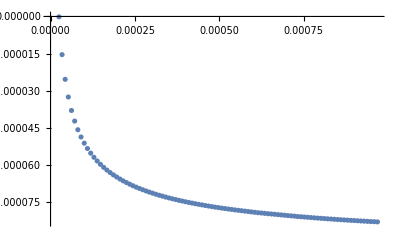

```mathematica
inloc=inputpr/.{h1->0,h2->0,R->1,h11->0.1,h12->0,η->.05,Δ->.0001,δ1->0,δ2->0,Jxv->.01,ϕxv->0,ϕyv->π};
aplot=ListPlot[Table[{Mean[Table[Abs[((Jy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jyv,0.00001,0.001,.00001}]]
```

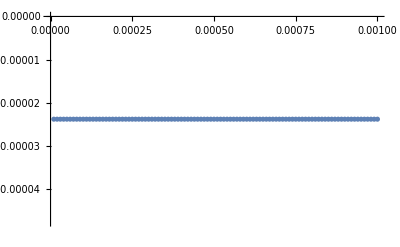

```mathematica
inloc=inputpr/.{h1->0,h2->0.1,R->1,h11->0,h12->0,η->.01,Δ->.0001,δ1->0,δ2->0,Jyv->.001,ϕxv->0,ϕyv->π};
aplot=ListPlot[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv,0.00001,0.001,.00001}]]
```

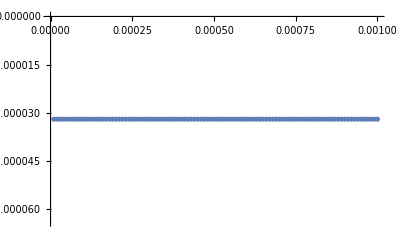

```mathematica
inloc=inputpr/.{h1->0.1,h2->0,R->1,h11->0,h12->0,η->.05,Δ->.0001,δ1->0,δ2->0,Jxv->.01,ϕxv->0,ϕyv->π};
aplot=ListPlot[Table[{Mean[Table[Abs[((Jy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jyv,0.00001,0.001,.00001}]]
```

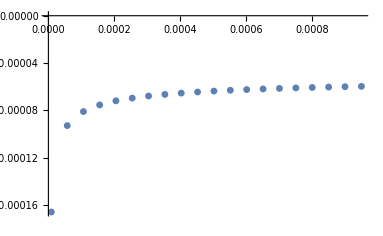

```mathematica
inloc=inputpr/.{h1->0,h2->0,R->1,h11->0.1,h12->0,η->.02,Δ->.0001,δ1->0,δ2->0,Jxv->.005,ϕxv->0,ϕyv->π};
aplot=ListPlot[Table[{Mean[Table[Abs[((Jy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jyv,0.00001,0.001,.00005}],PlotRange->All]
```

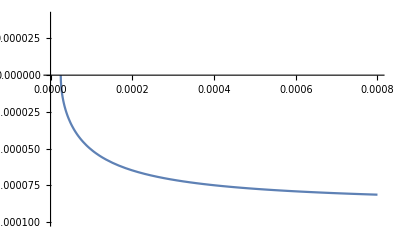

```mathematica
bplot=Plot[-((x-0.000025)/(1+6400(x-0.000025)))^(1/2)/140,{x,0.000025,.0008},PlotRange->{-.0001,0.00004}]
```

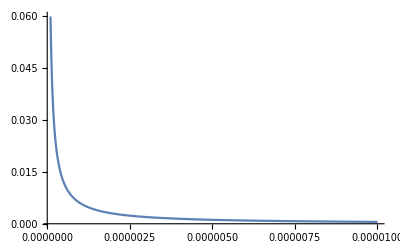

```mathematica
bplot=Plot[-(((x-0.0001(1-b))/x-1 b)/10000)/.{b->.4},{x,0.0000001,.00001},PlotRange->All]
```

```mathematica
N[Sqrt[(0.011125-0.005)/(0.011125-0.0001)]]
```

0.745356

```mathematica
(0.004/32)81+0.001
```

0.011125

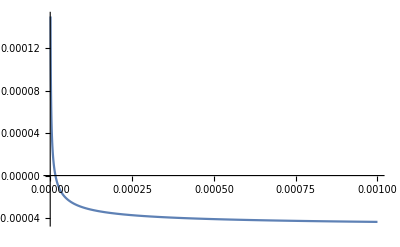

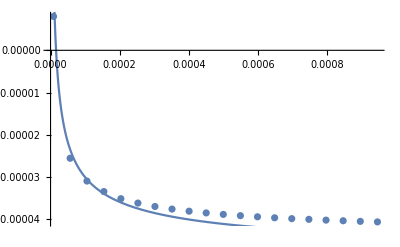

```mathematica
bplot=Plot[(0.4/Sqrt[x]-100)/(2000000),{x,0.000001,.001},PlotRange->All]
Show[{aplot,bplot}]
```

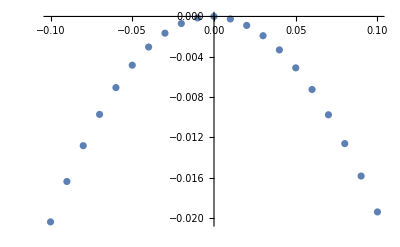

```mathematica
inloc=inputpr/.{h1->0,h2->f2v,R->1,h12->0,h11->0,η->0,Δ->.002,δ1->0,δ2->0,Jxv->.001,ϕxv->0,ϕyv->π};
ListPlot[Table[{f2v,(1/x Fit[Table[{Mean[Table[Abs[((Jy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jyv,0.001,0.009,.001}],{1,x},x])/.{x->10000}},{f2v,-.1,.1,0.01}]]
```

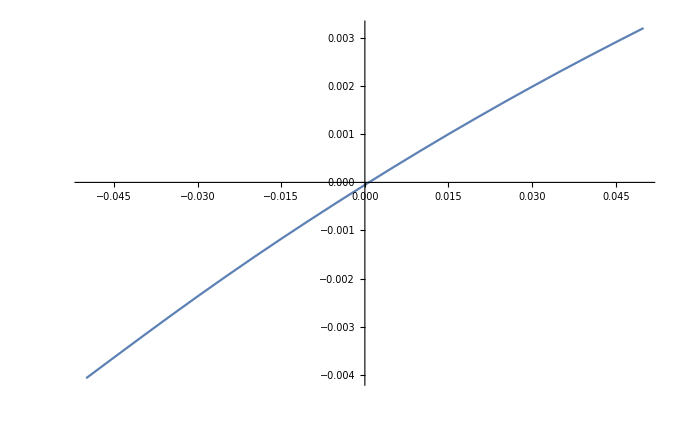

```mathematica
inloc=inputpr/.{h1->0,h2->f2v,R->1,h12->0.01,h11->0,η->0,Δ->.002,δ1->0,δ2->0,Jyv->.1,ϕxv->0,ϕyv->π};
ListPlot[Table[{f2v,(1/x Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv,0.001,0.009,.001}],{1,x},x])/.{x->1000000}},{f2v,-.05,.05,0.005}],Joined->True]
```

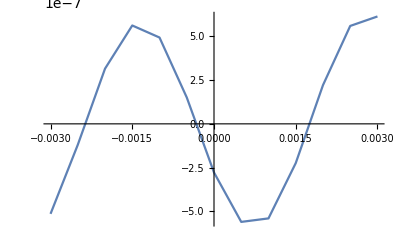

```mathematica
inloc=inputpr/.{h1->0,h2->0,R->1,h12->0.01,h11->0,η->0,Δ->f2v,δ1->0,δ2->0,Jyv->.1,ϕxv->0,ϕyv->π};
ListPlot[Table[{f2v,0.5 10^(-5)+( Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv,0.001,0.009,.001}],{1,x},x])/.{x->0}},{f2v,-.003,.003,0.0005}],Joined->True]
```

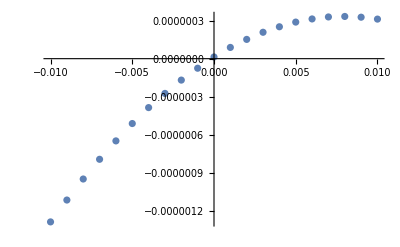

```mathematica
inloc=inputpr/.{h1->.0001,h2->.0001,R->1,h12->f2v,h11->.0001,η->.005,Δ->.0001,δ1->0,δ2->0,Jyv->.005,ϕxv->0,ϕyv->π};
ListPlot[Table[{f2v,(Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv,0.001,0.009,.001}],{1,x},x])/.{x->0}},{f2v,-.01,.01,0.001}]]
```

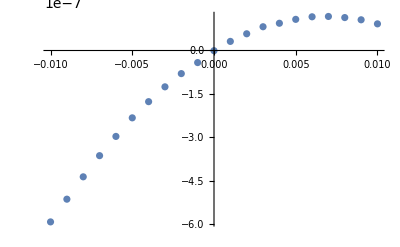

```mathematica
inloc=inputpr/.{h1->.0001,h2->.0001,R->1,h12->f2v,h11->.0001,η->.005,Δ->.0001,δ1->0,δ2->0,Jyv->.005,ϕxv->0,ϕyv->π};
ListPlot[Table[{f2v,(Fit[Table[{Mean[Table[Abs[((Jx[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->t1})],{t1,0,500,50}]],(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->500})-(((ϕy[t]/.Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,500}]])/.{t->0})))/500},{Jxv,0.001,0.009,.001}],{1,x},x])/.{x->0}},{f2v,-.01,.01,0.001}]]
```

```mathematica
0.001 - 5.6438
```

```mathematica
5.6438 Sqrt[5]
```

12.6199

```mathematica
13.25 - 0.001, .1
```

```mathematica
13.25 Sqrt[2]
```

18.7383

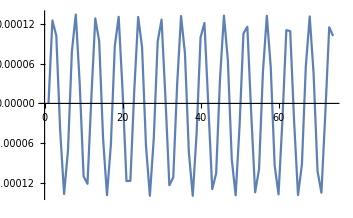

```mathematica
inloc=inputpr/.{h1->0,h2->0,R->1,h12->0.01,h11->0,η->.001,Δ->.05,δ1->0,δ2->0,Jxv->.001,ϕxv->0,ϕyv->π};
Table[ListPlot[Table[ϕx[t]/.Flatten[NDSolve[inloc/.{p->p,Jyv->0.001},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,73.8}]]/.{t->t1},{t1,0,73.8,1}],Joined->True],{p,.295,.295,0.001}]
```

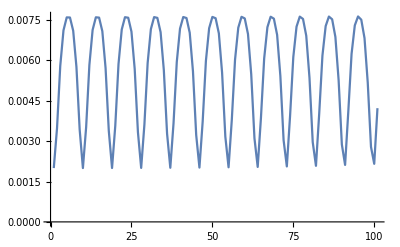

```mathematica
inloc=inputpr/.{h2->0,h1->7.02,R->1/π,h12->0,h11->0,η->0,Δ->0.1,δ1->0,δ2->0,Jxv->.002,ϕxv->0,ϕyv->0};
Table[ListPlot[Table[Jx[t]/.Flatten[NDSolve[inloc/.{p->p,Jyv->0.002},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100}]]/.{t->t1},{t1,0,100,1}],Joined->True],{p,.295,.295,0.001}]
```

```mathematica
N[1/Sqrt[3]]
```

0.57735

```mathematica
Sqrt[J]Abs[h11]~(2π/(3Sqrt[10]) Abs[(6Δ+η)])
Sqrt[J]Abs[h12]~(2π/(3Sqrt[10]) Abs[(6Δ-η)])
Sqrt[J]Abs[h1]~(π/2Abs[(η+2Δ)])
Sqrt[J]Abs[h2]~(π/2Abs[(-η+2Δ)])
```

```mathematica
4.6/1.3
```

3.53846

```mathematica
Solve[Sqrt[0.002] 7.02==a 0.1 2,a]
```

{{a→1.56972}}

```mathematica
2.7 2/3
```

1.8

```mathematica
(a /1.3+(a 2/3)/1.04)/.{a->2.7}
```

3.80769

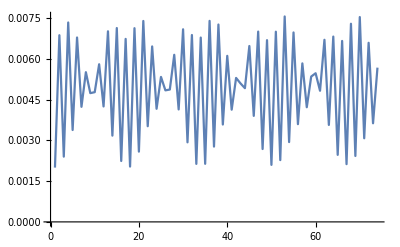

```mathematica
inloc=inputpr/.{h2->2.4 2π,h1->0.9 2π,R->1,h12->0,h11->2.7 2 π,η->0,Δ->0,δ1->0,δ2->0,Jxv->.002,ϕxv->0,ϕyv->0};
Table[ListPlot[Table[Jy[t]/.Flatten[NDSolve[inloc/.{p->p,Jyv->0.002},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,73.8}]]/.{t->t1},{t1,0,73.8,1}],Joined->True],{p,.295,.295,0.001}]
```

```mathematica
N[ArcTan[1/3]]
```

0.321751

```mathematica
Cos[0.3217505543966422]
```

0.948683

```mathematica
Sin[0.3217505543966422]
```

0.316228

```mathematica
расст =0.31622776601683794(3Δ+η)
```

```mathematica
π 0.31622776601683794
```

0.993459

```mathematica
1.57/π
```

0.499747

```mathematica
Simplify[Sin[ArcTan[x]]]
```

x/(√(1+x^2))

```mathematica
0.65/N[π/Sqrt[10]]
```

0.65428

```mathematica
0.65/π
```

0.206901

```mathematica
N[2π/(3Sqrt[10])]
```

0.662306